LQR增益矩阵 K = {{0.855836+0. ⅈ,0.316228+0. ⅈ}}

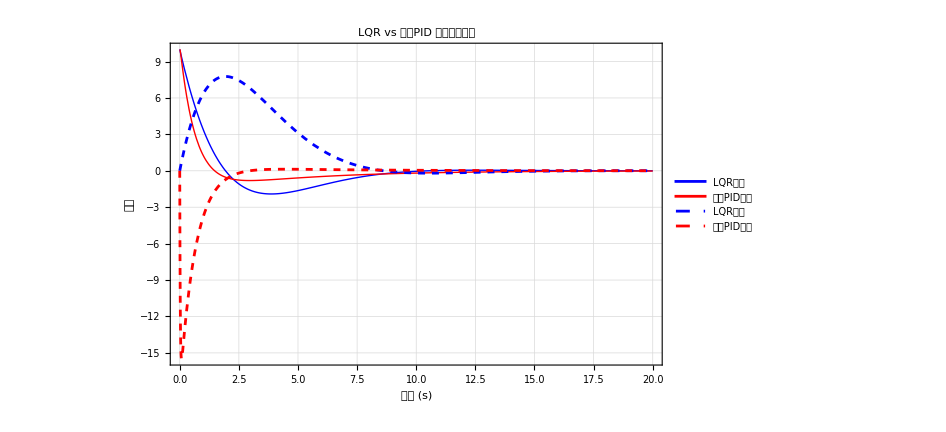

```mathematica
ClearAll["Global`*"]

(*系统参数*)
{a,b,c,d}={({{0, 0}, {1, 0}}),({{1}, {0}}),({{1, 0}, {0, 1}}),({{0}, {0}})};

(*LQR参数*)
{q, r} = {({{1, 0}, {0, 1}}), {{10}}};

(*串级PID参数*)Kp1=10;   (*外环比例增益*)
Ki1=2;    (*外环积分增益*)
Kd1=5;    (*外环微分增益*)
Kp2=8;    (*内环比例增益*)
Ki2=3;    (*内环积分增益*)

(*仿真参数*)
reference=0;      (*参考输入-调节到原点*)
initialPos=10;     (*初始位置*)
initialVel=0;   (*初始速度*)
tmax=20;          (*仿真时间*)

(* ==========LQR控制器==========*)
ssm=StateSpaceModel[{a,b,c,d}];
sspec=<|"InputModel"->ssm,"FeedbackInputs"->1|>;
K=LQRegulatorGains[sspec,{q,r}]//N;
closedSys=SystemsModelStateFeedbackConnect[ssm,K];
x0={initialPos,initialVel};

(*LQR初始条件响应-调节问题*)
lqrResponse=OutputResponse[{closedSys,x0},0,{t,0,tmax}];
lqrPosition=lqrResponse[[1]];
lqrVelocity=lqrResponse[[2]];

(* ==========串级PID控制器==========*)
cascadePID[kp1_,ki1_,kd1_,kp2_,ki2_,ref_,x0pos_,x0vel_,tmax_]:=Module[{sol},sol=NDSolve[{(*系统动态方程*)x1'[t]==x2[t],x2'[t]==kp2*(kp1*(ref-x1[t])+ki1*x3[t]+kd1*(-x2[t])-x2[t])+ki2*x4[t],(*积分项*)x3'[t]==ref-x1[t],x4'[t]==kp1*(ref-x1[t])+ki1*x3[t]+kd1*(-x2[t])-x2[t],(*初始条件*)x1[0]==x0pos,x2[0]==x0vel,x3[0]==0,x4[0]==0},{x1,x2,x3,x4},{t,0,tmax}];
If[sol==={},Print["串级PID求解失败！"];{{0,0,0,0}},{x1[t],x2[t],x3[t],x4[t]}/. sol[[1]]]];

{pidPosition,pidVelocity,int1,int2}=cascadePID[Kp1,Ki1,Kd1,Kp2,Ki2,reference,initialPos,initialVel,tmax];

(* ==========对比绘图==========*)

(*输出LQR增益矩阵*)
Print["LQR增益矩阵 K = ",K];

(*综合对比图*)
Plot[{lqrPosition,pidPosition,lqrVelocity,pidVelocity},{t,0,tmax},PlotRange->All,PlotStyle->{{Blue,Thick},{Red,Thick},{Blue,Dashed},{Red,Dashed}},PlotLegends->{"LQR位置","串级PID位置","LQR速度","串级PID速度"},PlotLabel->"LQR vs 串级PID 调节问题对比",FrameLabel->{"时间 (s)","状态"},Frame->True,GridLines->Automatic,ImageSize->700]
```